```mathematica
(*Needs["PacletManager`"]
PacletInstall[NotebookDirectory[]<>"packages/MaTeX-1.7.4.paclet"]*)
```

```mathematica
Needs["MaTeX`"]
MaTeX["x^2"]
```

-Graphics-

```mathematica
BOUND=5.25;
NPOINTS=30;
```

### Lyapunov function

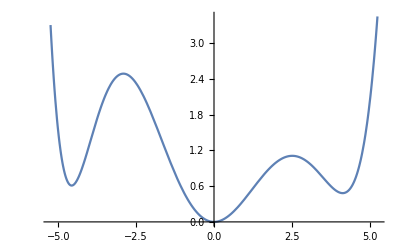

```mathematica
V[x_]:=a0+a1 x+a2 x^2+a3 x^3+a4 x^4+a5 x^5+a6 x^6+a7 x^7+a8 x^8
ansV=Solve[
{
V[0]==0,
V'[0]==0,
V''[0]==1,
V[2]==1,
V[4]==0.5,
V[5]==2,
V[-2]==1.8,
V[-4]==1.3,
V[-5]==1.5
}
,{a0,a1,a2,a3,a4,a5,a6,a7,a8}
];
Plot[V[x]/.ansV[[1]],{x,-BOUND,BOUND}]
```

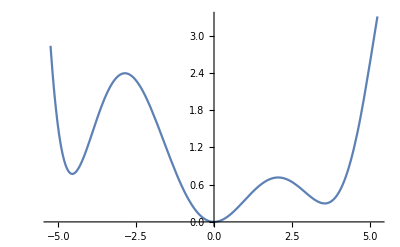

```mathematica
V[x_]:=a0+a1 x+a2 x^2+a3 x^3+a4 x^4+a5 x^5+a6 x^6+a7 x^7+a8 x^8
ansV=Solve[
{
V[0]==0,
V'[0]==0,
V''[0]==1,
V[1.5]==0.6,
V[3.5]==0.6 0.5,
V[4.5]==0.6 2,
V[-2]==1.8,
V[-4]==1.3,
V[-5]==1.5
}
,{a0,a1,a2,a3,a4,a5,a6,a7,a8}
];
Plot[V[x]/.ansV[[1]],{x,-BOUND,BOUND}]
```

### β function (α tilde in the paper): only non-decreasing function

```mathematica
(*not working some reason*)
(*β[x_]:=NMinValue[{V[z]/.ansV[[1]],z ∈Interval[{x,BOUND},{-BOUND,-x}]},z]*)
β[x_]:=NMinValue[{V[z]/.ansV[[1]],x≤ z ≤ BOUND||-BOUND≤ z ≤ -x},z]
```

β function takes a long time to plot: create interpolation function instead (easier to plot)

```mathematica
βinterpol=Interpolation[Table[{x,β[x]},{x,0,BOUND,BOUND/NPOINTS}]];
```

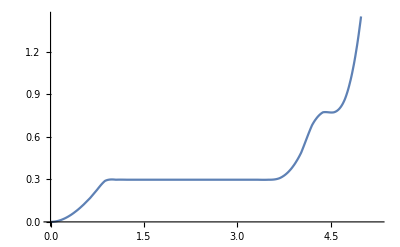

```mathematica
(*takes too long to plot*)
(*Plot[β[x],{x,0,BOUND}]*)
(*ListLinePlot[Table[β[x],{x,0,BOUND,BOUND/NPOINTS}]]*)
Plot[βinterpol[x],{x,0,BOUND}]
```

### α function: increasing function

```mathematica
(*takes too long*)
(*α[x_]:=1/(x+1)NIntegrate[β[z],{z,0,x}]*)
```

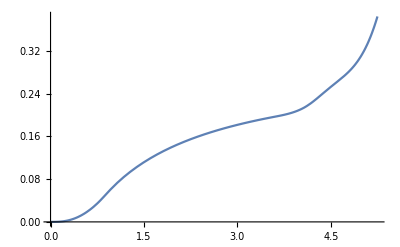

```mathematica
(*NDSolve[{α'[x]==1/(x+1)(β[x]-α[x]) && α[0]==0}, α[x], x]*)
α[x_]:=1/(x+1)NIntegrate[βinterpol[z],{z,0,x}] 
Plot[α[x],{x,0,BOUND}]
```

### plot all simultaneously

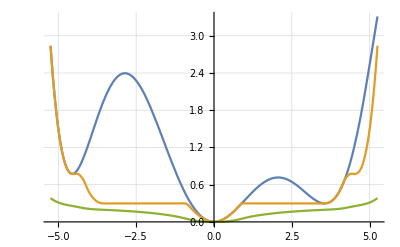

```mathematica
Plot[{
V[x]/.ansV[[1]],
βinterpol[Abs[x]],
α[Abs[x]]
},{x,-BOUND,BOUND},
PlotRange->All,
AxesLabel->{MaTeX["x"]},
Ticks->None,
PlotLegends->Placed[{
MaTeX["V(x)"],
MaTeX["\\tilde{\\alpha}(|x|)"],
MaTeX["\\alpha(|x|)"]
},
{0.6,0.8}
],
GridLines->Automatic
]
```

```mathematica
Export[NotebookDirectory[]<>"./figures/lower_bound_on_lyapunov_function.pdf",%];
```